```mathematica
Δ=2*0.5;(* 2 Rashba  Coupling times Subscript[p, F]*)
k=1;(* Fermi Wave Vector*)
u=0.3;(* Electron electron interaction Coulomb *)
a=Δ/u(2-u-2 √(1-u));(*lower limit for Dresselhaus Coupling*)
b=Δ/u(2-u+2 √(1-u));(*Upper limit for Dresselhaus Coupling*)
```

```mathematica
A1=Abs[(1-δ/Δ)] √(1-(u/2)/(1+(2*δ/Δ)/(u(1-δ/Δ)^2)));(*Subscript[ϵ, F]=(k^2 Subscript[v, F]^2)/4, Subscript[π, xx],Subscript[π, yy] spin susceptibility mode*)

A2=√((1-u)/(1-2u)((1-u)(1+(δ/Δ)^2)-√(u^2(1+(δ/Δ)^4)+2*(δ/Δ)^2((u-1)^2-2u+1))));
(*Subscript[ϵ, F]=(k^2 Subscript[v, F]^2)/4, Subscript[π, zz] spin susceptibility mode*)
A3=Abs[(1+δ/Δ)] √(1-(u/2)/(1-(2*δ/Δ)/(u(1+δ/Δ)^2)));(*Subscript[ϵ, F]=(k^2 Subscript[v, F]^2)/4 ,Subscript[π, xx],Subscript[π, yy] spin susceptibility mode valid with condition 1<u(α+β)^2/(4*α*β)*)
```

```mathematica
L5=Graphics[{Thickness[0.005],Circle[{.5,1.0},{.5,1.0}]}];
```

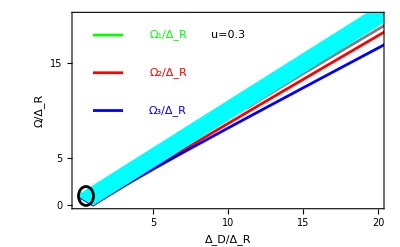

```mathematica
a=Plot[{A1,A2},{δ,0,25},PlotStyle->{{Thickness[0.005],Red},{Thickness[0.005],Blue}}];
b=Plot[A3,{δ,0,25},RegionFunction->Function[{δ},1<u(1+δ/Δ)^2/(4*δ/Δ)],PlotStyle->{Thickness[0.005],Gray}];
c=Plot[{Abs[(1+δ/Δ)],Abs[(1-δ/Δ)]},{δ,0,25},PlotStyle->{Cyan,Cyan},Filling->1->{2},FillingStyle->Cyan];
Show[a,b,c,L5,PlotRange->{{0,20},{0,20}},PlotRangePadding->0,Frame-> True,FrameLabel->{"\!\(Δ_D/Δ_R\)","\!\(Ω/Δ_R\)"},BaseStyle->{FontFamily->"Arial",20,SingleLetterItalics->True},FrameTicks->{{{0,5,15},Automatic},{{5,15,10,20},Automatic}},Epilog->{Thickness[0.005],Green,Line[{{1,18},{3,18}}],Text[" Ω_1/Δ_R",{6,18}],Thickness[0.005],Red,Line[{{1,14},{3,14}}],Text["Ω_2/Δ_R  ",{6,14}],
Thickness[0.005],Blue,Line[{{1,10},{3,10}}],Text[" Ω_3/Δ_R ",{6,10}],Thickness[0.005],Black,Text[" u=0.3 ",{10,18}]}, ImageSize->Scaled[0.585]]
```

```mathematica
Show[a,b,c,PlotRange->{{0,20},{0,20}},PlotRangePadding->0,Frame-> True,FrameStyle->Directive[Black,Thickness@.003],FrameLabel->{{None,"\!\(Ω/Δ_R\)"},{"\!\(Δ_D/Δ_R\)",None}},BaseStyle->{FontFamily->"Arial",20,Bold,SingleLetterItalics->True},FrameTicks->{{None,{0,8,16}},{{8,16},None}},Epilog->{Thickness[0.005],Gray,Text[" Ω_1",{4,18}],Thickness[0.005],Red,Text["Ω_2  ",{4.2,14}],
Thickness[0.003],Blue,Text[" Ω_3 ",{4,10}]},AspectRatio->1,PlotRangeClipping->True,ImageSize->Medium]
```

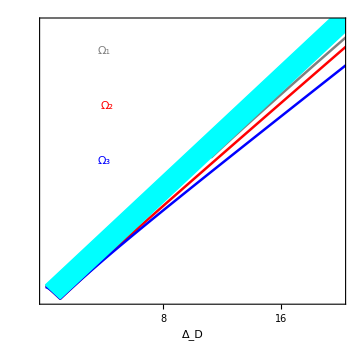

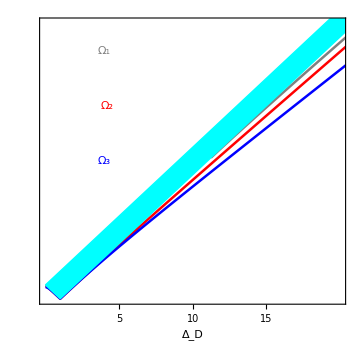

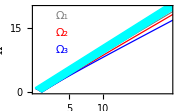

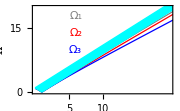

```mathematica
DL=Show[L4,L5,L6,PlotRange->{{0.001,.2},{.51,.9}},Frame-> True,FrameStyle->Directive[Black,Thickness@.003],FrameLabel->{"\!\(Δ_z/Δ_R\)","\!\(Ω/Δ_R\)"},BaseStyle->{FontFamily->"Arial",6,SingleLetterItalics->True},FrameTicks->{{{.55,.65,.75,0.85},None},{{0.02,0.06,0.1,0.14,0.18},None}},Epilog->{Thickness[0.003],Black,Text[" Δ_D/Δ_R = 0.25 ",{0.0507,0.8}],Thickness[0.003],Red,Text[" Ω_2",{0.0207,.67}],Thickness[0.003],Blue,Text["Ω_3  ",{0.023,.59}]}, ImageSize->Small]
```

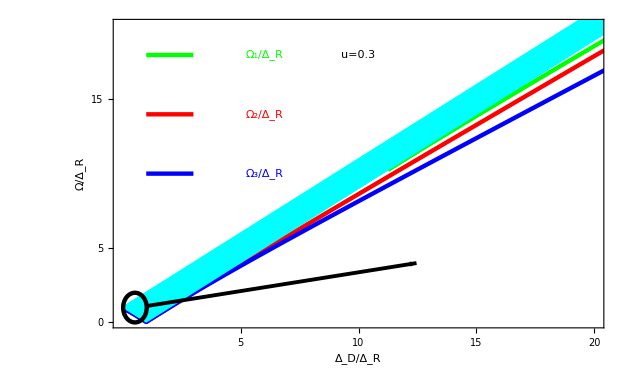

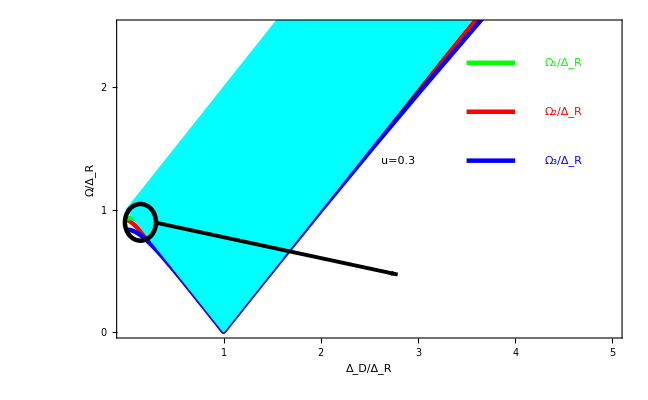

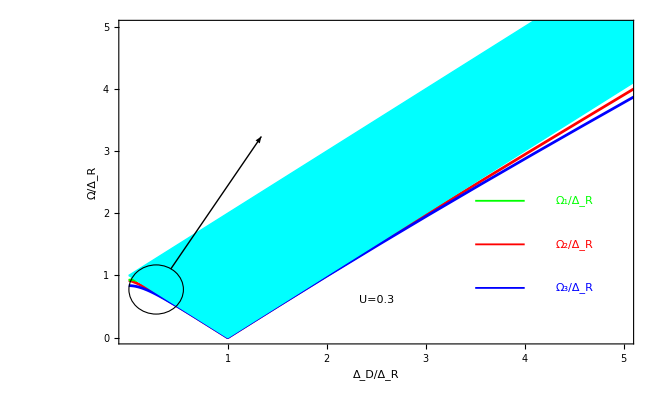

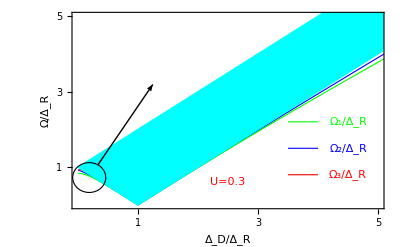

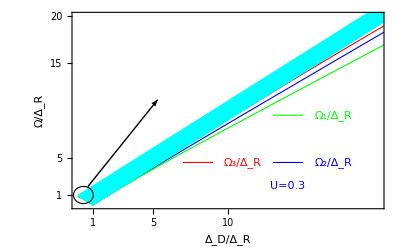

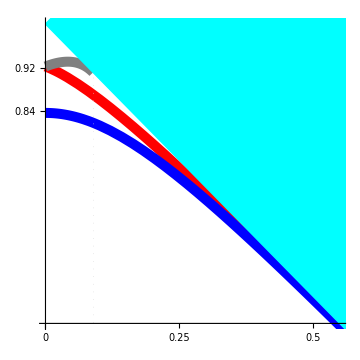

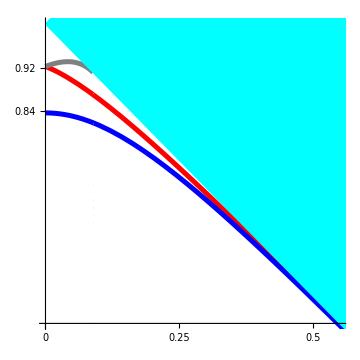

```mathematica
a=Plot[{A1,A2},{δ,0,1},PlotStyle->{{Thickness[0.02],Red},{Thickness[0.02],Blue}}];
b=Plot[A3,{δ,0,1},RegionFunction->Function[{δ},1<u(1+δ/Δ)^2/(4*δ/Δ)],PlotStyle->{Thickness[0.02],Gray}];
c=Plot[{Abs[(1+δ/Δ)],Abs[(1-δ/Δ)]},{δ,0,1},PlotStyle->{Cyan,Cyan},Filling->1->{2},FillingStyle->Cyan];
Show[a,b,c,PlotRange->{{0,.55},{.45,1}},AxesOrigin->{0,0.45},Axes-> True,Ticks->{{0,.25,.5},{0,.84,.92}},TicksStyle->Directive[Bold,FontSize->16],PlotRange->{{0,4},{0,3}},ImageSize->Medium,Background->White,PlotRangePadding->-0.00000,BaseStyle->{FontFamily->"Arial",16,SingleLetterItalics->True},GridLines->{{{0.09,Dotted}},{-5,5}},AspectRatio->1,PlotRangeClipping->True,ImageSize->Medium]
```

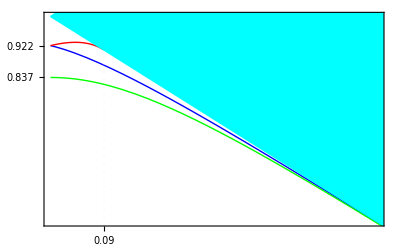

```mathematica
a=Plot[{A1,A2},{δ,0,1},PlotStyle->{Blue,Green}];
b=Plot[A3,{δ,0,1},RegionFunction->Function[{δ},1<u(1+δ/Δ)^2/(4*δ/Δ)],PlotStyle->Red];
c=Plot[{Abs[(1+δ/Δ)],Abs[(1-δ/Δ)]},{δ,0,1},PlotStyle->{Cyan,Cyan},Filling->1->{2},FillingStyle->Cyan];
Show[a,b,c,PlotRange->{{0,.55},{.45,1}},Frame-> True,BaseStyle->{FontFamily->"Arial",20,SingleLetterItalics->True},FrameTicks->{{{.837, .922},Automatic},{{0.09},Automatic}},GridLines->{{{0.09,Dotted}},{-5,5}},AxesOrigin->{0,0},Epilog->{Thick,Green,Line[{{0,35},{1,35}}],Text[" Ω_1/Δ_D",{2,35}],Thick,Red,Line[{{0,25},{1,25}}],Text["Ω_2/Δ_D  ",{2,25}],
Thick,Gray,Line[{{0,15},{1,15}}],Text[" Ω_3/Δ_D ",{2,15}]}, ImageSize->Scaled[0.75]]
```